```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
runnumber=100;
threshold=0.0;
max=9999;
```

71

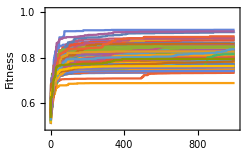

b.eps

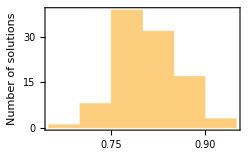

b_hist.eps

```mathematica
exp="../EvolutionData/Offset/C";
maxfit=0.0;
maxind =-1;
allgens={};
allfit={};
bestgen={};
For[i=0, i<runnumber, i++,
file = StringJoin[exp,"/",ToString[i], "/fitness.dat"];
x = Import[file];
y = Transpose[x];
allgens=Append[allgens,y[[2]]];
allfit=Append[allfit,Last[y[[2]]]];
If[Last[y[[2]]]>maxfit,maxfit=Last[y[[2]]];maxind=i;];
If[Last[y[[2]]]>threshold,
file = StringJoin[exp,"/",ToString[i], "/best.gen.dat"];
x = Flatten[Import[file]];
bestgen=Append[bestgen,x];
];
];

maxind
ListLinePlot[Sqrt[allgens],PlotRange->{{-10,1010},{0.49,1.01}},Frame->True,FrameLabel->{"Generations","Fitness"},ImageSize->250]
Export["b.eps",%]
Histogram[Sqrt[allfit],Frame->True,FrameLabel->{"Fitness","Number of solutions"},ImageSize->250]
Export["b_hist.eps",%]
```

```mathematica
Sort[Table[{x-1,allfit[[x]]},{x,1,100}],#1[[2]]>#2[[2]]&]
```

{{71,0.851567},{98,0.839009},{90,0.836074},{93,0.799239},{73,0.791642},{31,0.784444},{43,0.782617},{11,0.77244},{25,0.771709},{1,0.767336},{4,0.750017},{55,0.748841},{66,0.747398},{21,0.746773},{60,0.74559},{80,0.740617},{2,0.729342},{88,0.729136},{0,0.725583},{62,0.725537},{92,0.721889},{32,0.715766},{77,0.713377},{42,0.71295},{26,0.701085},{96,0.700514},{23,0.696383},{68,0.695358},{10,0.694167},{16,0.691577},{3,0.68935},{91,0.684609},{51,0.684254},{35,0.682217},{47,0.675829},{12,0.67307},{9,0.670142},{22,0.666509},{61,0.665103},{89,0.664278},{45,0.662244},{54,0.661918},{87,0.659245},{56,0.656064},{20,0.656021},{39,0.654539},{34,0.650191},{29,0.649552},{53,0.649172},{78,0.647702},{28,0.646085},{76,0.644131},{40,0.63932},{30,0.637957},{83,0.63431},{69,0.633853},{85,0.633206},{99,0.630475},{49,0.629267},{13,0.628587},{18,0.627432},{15,0.624382},{64,0.624151},{5,0.622858},{81,0.621191},{7,0.618893},{37,0.616822},{57,0.616226},{95,0.614477},{65,0.612651},{67,0.607693},{72,0.606697},{8,0.599353},{24,0.59867},{14,0.598649},{58,0.595362},{75,0.594641},{36,0.59038},{50,0.586334},{74,0.583891},{97,0.581923},{79,0.579361},{52,0.578005},{84,0.57645},{17,0.571877},{94,0.571295},{70,0.570842},{44,0.570084},{82,0.565866},{38,0.564682},{63,0.562954},{41,0.5599},{46,0.557354},{59,0.557236},{19,0.54927},{86,0.548562},{33,0.546754},{6,0.541358},{48,0.536756},{27,0.472777}}

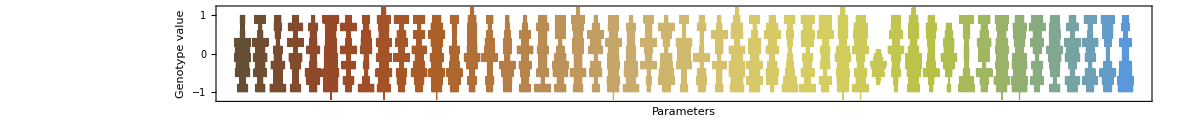

Parameters.eps

```mathematica
DistributionChart[Transpose[bestgen],ChartStyle->"SouthwestColors",ChartElementFunction->"HistogramDensity",Frame->True,AspectRatio->1/10,FrameLabel->{"Parameters","Genotype value"},ImageSize->1200]
Export["Parameters.eps",%]
```